# Lattice Simulation

## Bloch wave basis, periodic potential

#### Dispersion relation / Energy bands

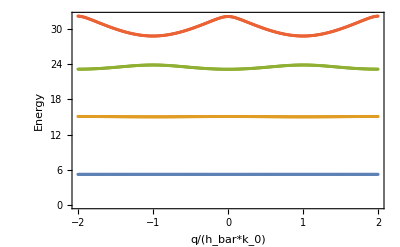

```mathematica
Hij[V0_,q_,i_,j_]:=If[i==j,(2i+q)^2+V0/2,If[Abs[i-j]==1,-1/4 V0,0]]; (*Hamiltonian matrix elements*)
lMax=4;  (*maximum absolute value of bloch wave index*)
H[V0_,q_]:=Table[Hij[V0,q,i,j],{i,-lMax,lMax},{j,-lMax,lMax}] (* Hamiltonian matrix form *)
eigenvals[V_,q_]:=Sort[N[Eigenvalues[H[V,q]]]] (* Get eigenvalues of matrix (eigenenergies) *)
V0=30;
qlist=Range[-2,2,0.01];(*quasi-momentum list from -q0 to q0*)
EnergyMx=Map[eigenvals[V0,#]&,qlist];(* list of lists: energy eigenvalues for each quasi momentum value q *)
nband=4;(*Plot to nth band, which should be smaller than (2*lmax+1)*)
FigBS2=ListPlot[Table[Transpose[{qlist,EnergyMx[[All,iband]]}],{iband,1,nband}],Frame->True,FrameLabel->{"q/(h_bar*k_0)","Energy"}](*listplot is fast*)
```

#### Band Gaps

```mathematica
BandGapMin=Table[Min[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*min band gap 1-2, 1-3, 1-4, ... till 1-nband *)
BandGapMax=Table[Max[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*max band gap ..*)
BandGapMean=Table[Mean[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*mean band gap ..*)
BandGapTb=Transpose[{BandGapMin,BandGapMax,BandGapMean}];
FirstColumn = Prepend[Table["1-"<>ToString[j],{j,2,nband}],"Band Gap"];
DataColumns = Prepend[BandGapTb,{"Min","Max","Mean"}];
BandGapTbLabel=MapThread[Prepend,{DataColumns,FirstColumn}];
Grid[BandGapTbLabel,Dividers->{False,All}]
```

Band Gap | Min | Max | Mean
1-2 | 9.79758 | 9.86342 | 9.82918
1-3 | 17.9103 | 18.6333 | 18.2552
1-4 | 23.5696 | 26.962 | 24.9774

#### Tunneling

```mathematica
BandMax=Map[Max[EnergyMx[[All,#]]]&,Range[1,nband]]; (* max energy for each band *)
BandMin=Map[Min[EnergyMx[[All,#]]]&,Range[1,nband]];(* min energy for each band *)
BandWidth = BandMax-BandMin;(* band width for each band *)
Tunneling=BandWidth/4; (* saw in Dieter Jaksch PRL paper 1998, which is valid both for all bands if the band is deep enough such as 5Er*)
FirstColumn = Prepend[Table["Band"<>ToString[j],{j,1,nband}]," "];
DataColumns = Prepend[Tunneling,"Tunneling"];
Grid[Transpose[{FirstColumn,DataColumns}],Dividers->{False,All}]
```

| Tunneling
Band1 | 0.000471594
Band2 | 0.0160947
Band3 | 0.181222
Band4 | 0.847718

#### Bloch Waves

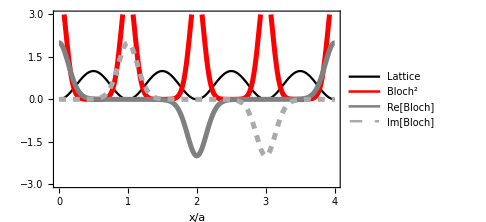
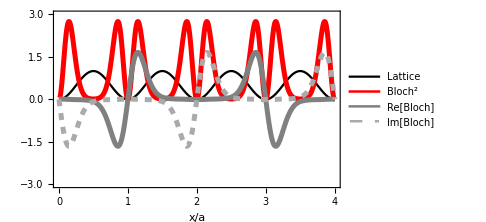
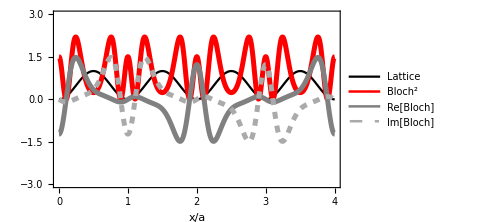
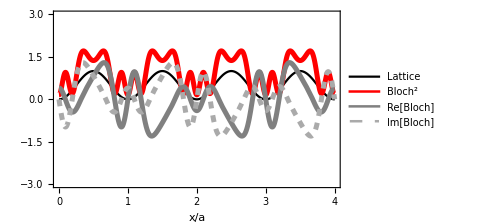

```mathematica
EV[V_,q_,l_]:=Sort[Transpose[Chop[N[Eigensystem[H[V,q]]]]]] [[l,2]]; (* Get the l th eigen vector of H , there are 2*lmax + 1 in total*)
EVNormed[V_,q_,l_]:=Module[{tmp=EV[V,q,l]},(tmp/Norm[tmp])] ; (* Get normed l th eigen vector of H, gives 2*lmax+1 probabilities of different Bloch wave states *)
Bloch[x_,V_,q_,l_]:=Sum[Exp[π*I (q+2n) x]*EVNormed[V,q,l][[n+lMax+1]],{n,-lMax,lMax}]; (* Bloch wave is summation of plane waves *)(*should we use cutoff jMax or smaller one instead??*)
q=0.5;
oneoverq= If[q>0,1/q,3];
BRe[x_]={Re[ Bloch[x,V0,q,1]],Re[ Bloch[x,V0,q,2]], Re[ Bloch[x,V0,q,3]], Re[ Bloch[x,V0,q,4]]};
BIm[x_]={Im[ Bloch[x,V0,q,1]],Im[ Bloch[x,V0,q,2]], Im[ Bloch[x,V0,q,3]], Im[ Bloch[x,V0,q,4]]};
BNorm[x_]={Norm[ Bloch[x,V0,q,1]],Norm[Bloch[x,V0,q,2]], Norm[Bloch[x,V0,q,3]], Norm[ Bloch[x,V0,q,4]]};
Table[Plot[{Sin[π*x]^2,(BNorm[x]^2)[[i]],BRe[x][[i]],BIm[x][[i]]},{x,0,2*oneoverq},Frame->True,Axes->False,FrameLabel->{"x/a"},PlotRange->{-3,3},PlotLegends->{"Lattice","Bloch^2","Re[Bloch]","Im[Bloch]"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}, ImageSize->Medium],{i,1,4}]
```

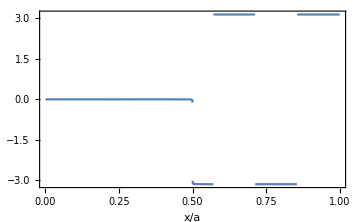
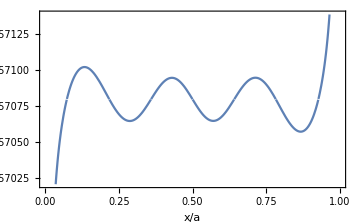
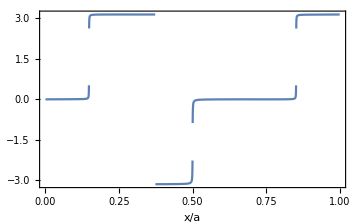
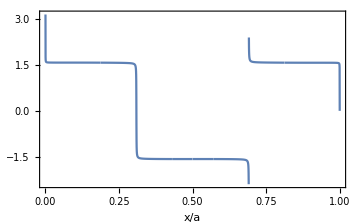

0

```mathematica
q=1;
oneoverq= If[q>0,1/q,3];
BArg[x_] = {Arg[Bloch[x,V0,q,1]],Arg[Bloch[x,V0,q,2]], Arg[Bloch[x,V0,q,3]], Arg[Bloch[x,V0,q,4]]};
Table[Plot[Chop[BArg[x][[i]]], {x, 0,oneoverq}, Frame->True,Axes->False,FrameLabel->{"x/a"}, ImageSize->Medium], {i, 1, 4}]
Arg[Bloch[0,V0,1,2]]
```

#### Wannier Functions

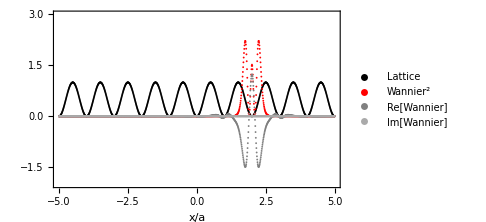

```mathematica
V0 = 30;
wpos = 2;
PhaseFactor[V_,q_,l_]:= If[OddQ[l],Arg[Bloch[0,V,q,l]],Arg[Bloch[0.25,V,q,l]]];
(* for odd bands, take phase factor at x = 0. If l is even, take phase factor at x = 0.25 *)(*force phase at x=0 equals to 0 for every Bloch waves for odd band and phase at x=0.25 (or values close to 0.13) equals to 0 for even band. It just Works!!*)
qqstep=0.1;
Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,qqstep}]    *    (qqstep/2)    -     1/2(Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2)
(*numerically integrate q from -1 to 1, however -1 and 1 are the same and we should deduct one*)
(*x: position, V: lattice depth, l: nth band, xi: wannier function at lattice site xi, which should be an integer*)
(*Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*SignFactor[V,q,l]*Bloch[x,V,q,l],{q,-1,1,qqstep}]*(qqstep/2)-1/2(Sum[Exp[π*I*q*(-xi)]*SignFactor[V,q,l]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2)*)
nWannier=3;(*1st, 2nd, 3rd band*)(* which energy band are we looking at *)
xxstep=0.01;

xlist=Range[-5,5,xxstep]; (* doesnt include max *)
wlist = Wannier[xlist,V0,nWannier,wpos];
ltslist=Sin[π*xlist]^2;(*lattice potential*)
wlistNorm=wlist/√Total[Re[wlist]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm]^2}],Transpose[{xlist,Re[wlistNorm]}],Transpose[{xlist,Im[wlistNorm]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","Wannier^2","Re[Wannier]","Im[Wannier]"},PlotRange->{-2,3}, PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}, ImageSize->Medium]
```

#### Hubbard parameters

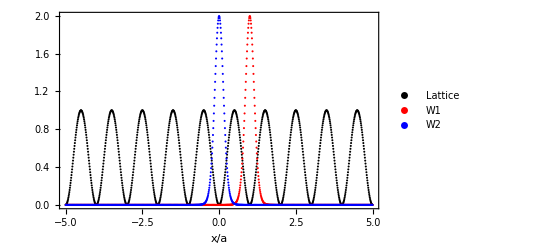

Interaction Energy: 0.169839

Hopping: -0.000470499

Interaction/Hopping: -360.976

| Tunneling
Band1 | 0.000471594
Band2 | 0.0160947
Band3 | 0.181222
Band4 | 0.847718

```mathematica
a0=5.29*10^-11;(*Bohr radius*)
ℏ=1/(2π)*6.626*10^-34;(*reduced Planck constant*)
mK39=39*1.66*10^-27;(* mass of K39*)
aK39=139*a0;(*scattering length for K39 at B=0. cited from https://arxiv.org/pdf/0705.3036.pdf, or simply sum up all the strength of Feshbach resonances*)
λLatK39=725*10^-9;(*725 lattice wavelength*)
k0K39=(2π)/λLatK39;(*lattice wave number*)
ErK39=ℏ^2 k0K39^2/(2*mK39);(*recoil energy*)

gcontact=(4π ℏ^2)/mK39*aK39;

Uint=gcontact/ErK39*(π/k0K39)^-3*Total[(Re[wlist])^4*xxstep]^3;(*for 3D cubic lattice in units of Er*)
xxstep=0.01;

xlist=Range[-5,5,xxstep]; (* doesnt include max *)
nWannier1=1;
nWannier2 = 1;
V0 = 30;
wlist1 = Wannier[xlist,V0,nWannier1,1];
wlist2 = Wannier[xlist,V0,nWannier2,0];(*wannier function at x=1, nearest neighbor*)
wlistNorm1=wlist1/√Total[Re[wlist1]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
wlistNorm2=wlist2/√Total[Re[wlist2]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm1]}],Transpose[{xlist,Re[wlistNorm2]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","W1","W2"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Blue}}]

dwlist=(wlist1[[1;;-3]]+wlist1[[3;;-1]]-2*wlist1[[2;;-2]])/xxstep^2/π^2;(*-ℏ^2/(2m)∂/(∂^2 x) in Hamiltonian and here we use Er as units and wannier function is dimensionless, -ℏ^2/(2m)∂/(∂^2 x)=-(ℏ^2 a^2)/(2m)∂/(∂^2 (x/a))= -(ℏ^2 k0^2)/(2m)∂/(∂^2 (x/a))1/π^2=Er ∂/(∂^2 (x/a))1/π^2*)
Jhop=(Chop[-Total[Re[wlist2[[2;;-2]]]*Re[dwlist]*xxstep]+Total[V0*ltslist*Re[wlist1]*Re[wlist2]*xxstep]]);(*Lattice tunnelling elements in units of Er. This result is consistent with this value of bandwidth/4, or slightly lower*)
Print["Interaction Energy: ", Uint]
Print["Hopping: ", Jhop]
Print["Interaction/Hopping: ", Uint/Jhop]
Grid[Transpose[{FirstColumn,DataColumns}],Dividers->{False,All}]
```

## Bloch wave basis, periodic potential + linear term

#### Dispersion relation